```mathematica
Get["/home/garofalo/programs/qct/qct.m"]
```

QuarkContractionTool (QCT)

```mathematica
piplus[x_,a_,α_,β_]=FieldB[d,a,α,x]**Gamma5 [SI[{α,β}]]**Field[u,a,β,x];
piplusD[x_,a_,α_,β_]=-FieldB[u,a,α,x]**Gamma5 [SI[{α,β}]]**Field[d,a,β,x];
pi0[x_,a_,α_,β_]=(1/(√2))**(FieldB[u,a,α,x]**Gamma5 [SI[{α,β}]]**Field[u,a,β,x]-FieldB[d,a,α,x]**Gamma5 [SI[{α,β}]]**Field[d,a,β,x]);
pi0D[x_,a_,α_,β_]=-(1/(√2))**(FieldB[u,a,α,x]**Gamma5 [SI[{α,β}]]**Field[u,a,β,x]
-
FieldB[d,a,α,x]**Gamma5 [SI[{α,β}]]**Field[d,a,β,x]);
piminus[x_,a_,α_,β_]=FieldB[u,a,α,x]**Gamma5 [SI[{α,β}]]**Field[d,a,β,x];
piminusD[x_,a_,α_,β_]=-FieldB[d,a,α,x]**Gamma5 [SI[{α,β}]]**Field[u,a,β,x];
(*piplus[x_]=FieldB[d,a,α,x]**Gamma5 [SI[{α,β}]]**Field[u,a,β,x];
piplusD[x_]=-FieldB[u,a,α,x]**Gamma5 [SI[{α,β}]]**Field[d,a,β,x];
pi0[x_]=1/(√2)**(FieldB[u,a,α,x]**Gamma5 [SI[{α,β}]]**Field[u,a,β,x]-FieldB[d,a,α,x]**Gamma5 [SI[{α,β}]]**Field[d,a,β,x]);
pi0D[x_]=1/(√2)**(FieldB[u,a,α,x]**Gamma5 [SI[{α,β}]]**Field[u,a,β,x]
-
FieldB[d,a,α,x]**Gamma5 [SI[{α,β}]]**Field[d,a,β,x]);
piminus[x_]=FieldB[u,a,α,x]**Gamma5 [SI[{α,β}]]**Field[d,a,β,x];
piminusD[x_]=-FieldB[d,a,α,x]**Gamma5 [SI[{α,β}]]**Field[u,a,β,x];
*)
```

-Gamma5[SI[{α,β}]]^2 DE[{u,u},{0,0}][CI[{a,a}],SI[{β,α}]] DE[{u,u},{t,t}][CI[{a,a}],SI[{β,α}]]+Gamma5[SI[{α,β}]]^2 (-DE[{u,u},{0,t}][CI[{a,a}],SI[{β,α}]] DE[{u,u},{t,0}][CI[{a,a}],SI[{β,α}]]+DE[{u,u},{0,0}][CI[{a,a}],SI[{β,α}]] DE[{u,u},{t,t}][CI[{a,a}],SI[{β,α}]])

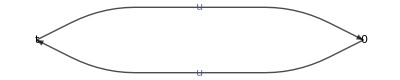

-Gamma5[SI[{α,β}]]^2 trace[transposeSpin[DE[{u,u},{t,0}]].DE[{u,u},{0,t}]]

```mathematica
pipi=WickContract[pi0[t]**pi0D[0]]/.{d,d}->{u,u}
GraphWC[pipi]
QuarkContract[pipi]
```

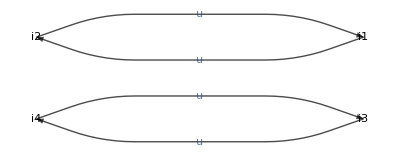
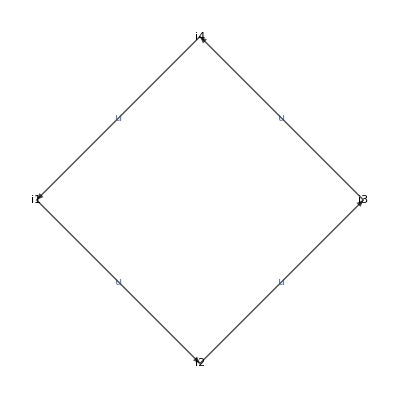
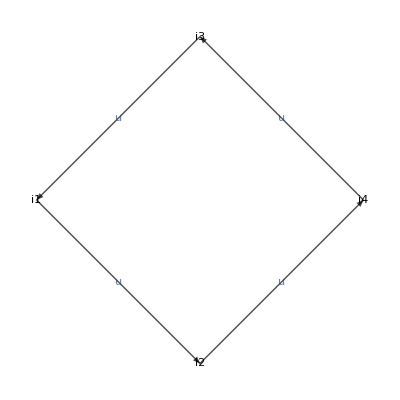
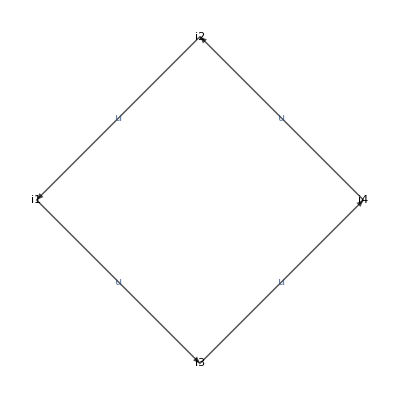
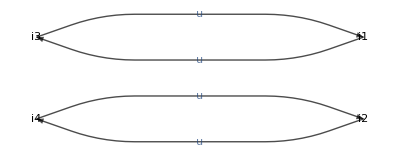
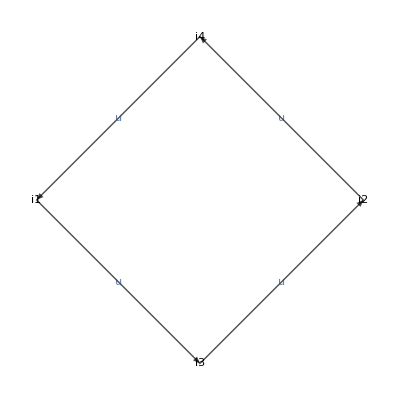
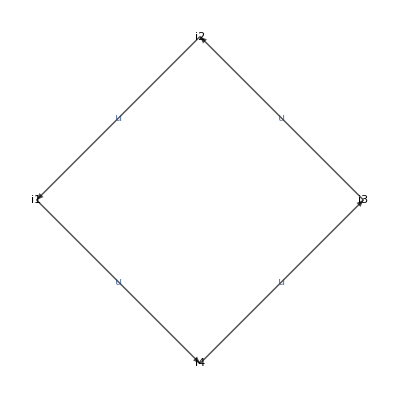
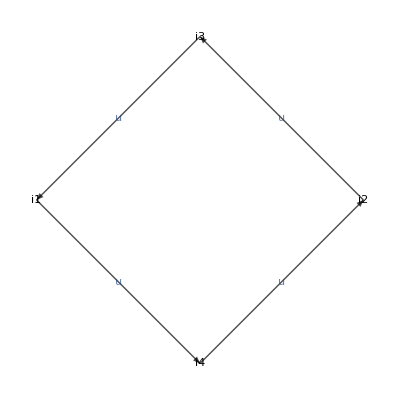

1/2 Gamma5[SI[{α,β}]]^4 (2 trace[Transpose[DE[{u,u},{i4,i1}]].DE[{u,u},{i3,i2}].transposeSpin[DE[{u,u},{i2,i3}]].DE[{u,u},{i1,i4}]]+trace[Transpose[DE[{u,u},{i4,i1}]].DE[{u,u},{i3,i2}].transposeSpin[DE[{u,u},{i2,i4}]].DE[{u,u},{i1,i3}]]-3 trace[Transpose[DE[{u,u},{i4,i1}]].DE[{u,u},{i3,i4}].transposeSpin[DE[{u,u},{i2,i3}]].DE[{u,u},{i1,i2}]]+trace[Transpose[DE[{u,u},{i4,i2}]].DE[{u,u},{i3,i1}].transposeSpin[DE[{u,u},{i2,i3}]].DE[{u,u},{i1,i4}]]+2 trace[Transpose[DE[{u,u},{i4,i2}]].DE[{u,u},{i3,i1}].transposeSpin[DE[{u,u},{i2,i4}]].DE[{u,u},{i1,i3}]]-3 trace[Transpose[DE[{u,u},{i4,i2}]].DE[{u,u},{i3,i4}].transposeSpin[DE[{u,u},{i2,i1}]].DE[{u,u},{i1,i3}]]-3 trace[Transpose[DE[{u,u},{i4,i3}]].DE[{u,u},{i3,i1}].transposeSpin[DE[{u,u},{i2,i4}]].DE[{u,u},{i1,i2}]]-3 trace[Transpose[DE[{u,u},{i4,i3}]].DE[{u,u},{i3,i2}].transposeSpin[DE[{u,u},{i2,i1}]].DE[{u,u},{i1,i4}]]+6 trace[Transpose[DE[{u,u},{i4,i3}]].DE[{u,u},{i3,i4}].transposeSpin[DE[{u,u},{i2,i1}]].DE[{u,u},{i1,i2}]])

```mathematica
O0=(1/(√3))**(piplus[i1]**piminus[i2]+piminus[i1]**piplus[i2]+pi0[i1]**pi0[i2] );
Ot=(1/(√3))**(piplusD[i3]**piminusD[i4]+piminusD[i3]**piplusD[i4]+pi0D[i3]**pi0D[i4] );
pipi=WickContract[O0**Ot]/.{d,d}->{u,u}
GraphWC[pipi]
Simplify[QuarkContract[pipi]]
```

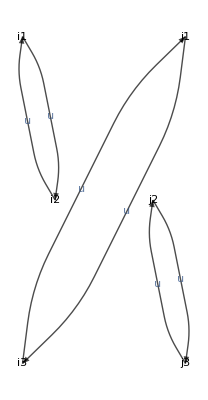
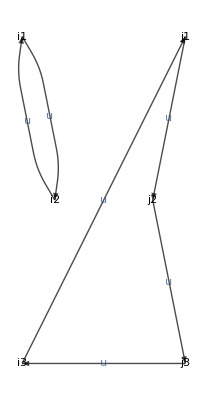
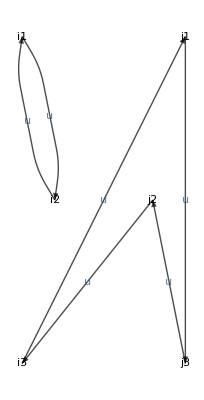
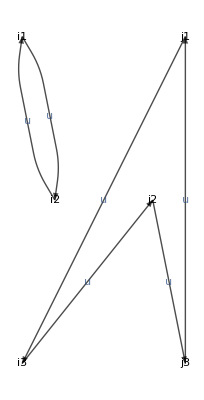
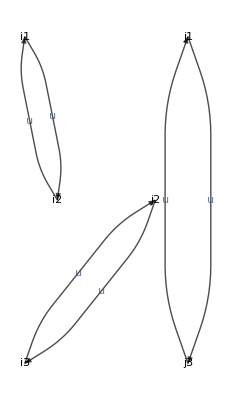
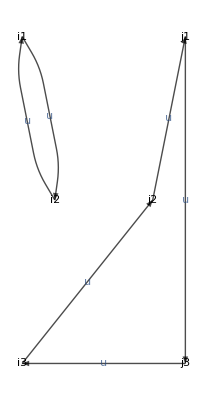
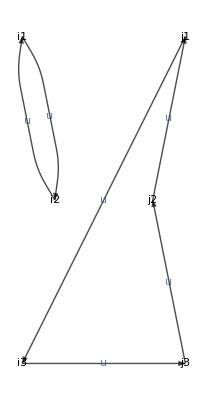
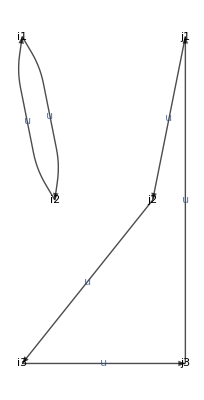
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pipipi[i1_,i2_,i3_]=(1/(√6))**(+piplus[i1,a1,b1,c1]**pi0[i2,a2,b2,c2]**piminus[i3,a3,b3,c3]
-piplus[i1,a1,b1,c1]**pi0[i3,a2,b2,c2]**piminus[i2,a3,b3,c3]
-piplus[i2,a1,b1,c1]**pi0[i1,a2,b2,c2]**piminus[i3,a3,b3,c3]
+piplus[i3,a1,b1,c1]**pi0[i1,a2,b2,c2]**piminus[i2,a3,b3,c3]
-piplus[i3,a1,b1,c1]**pi0[i2,a2,b2,c2]**piminus[i1,a3,b3,c3]
+piplus[i2,a1,b1,c1]**pi0[i3,a2,b2,c2]**piminus[i1,a3,b3,c3]
);
pipipiD[i1_,i2_,i3_]=(1/(√6))**(+piplusD[i1,a4,b4,c4]**pi0D[i2,a5,b5,c5]**piminusD[i3,a6,b6,c6]
-piplusD[i1,a4,b4,c4]**pi0D[i3,a5,b5,c5]**piminusD[i2,a6,b6,c6]
-piplusD[i2,a4,b4,c4]**pi0D[i1,a5,b5,c5]**piminusD[i3,a6,b6,c6]
+piplusD[i3,a4,b4,c4]**pi0D[i1,a5,b5,c5]**piminusD[i2,a6,b6,c6]
-piplusD[i3,a4,b4,c4]**pi0D[i2,a5,b5,c5]**piminusD[i1,a6,b6,c6]
+piplusD[i2,a4,b4,c4]**pi0D[i3,a5,b5,c5]**piminusD[i1,a6,b6,c6]
);
(*pipipi[i1_,i2_,i3_]=1/(√6)**(+piplus[i1]**pi0[i2]**piminus[i3]
-piplus[i1]**pi0[i3]**piminus[i2]
-piplus[i2]**pi0[i1]**piminus[i3]
+piplus[i3]**pi0[i1]**piminus[i2]
-piplus[i3]**pi0[i2]**piminus[i1]
+piplus[i2]**pi0[i3]**piminus[i1]
);
pipipiD[i1_,i2_,i3_]=1/(√6)**(+piplusD[i1]**pi0D[i2]**piminusD[i3]
-piplusD[i1]**pi0D[i3]**piminusD[i2]
-piplusD[i2]**pi0D[i1]**piminusD[i3]
+piplusD[i3]**pi0D[i1]**piminusD[i2]
-piplusD[i3]**pi0D[i2]**piminusD[i1]
+piplusD[i2]**pi0D[i3]**piminusD[i1]
);*)
contr3pi3pi=WickContract[pipipi[i1,i2,i3]**pipipiD[j1,j2,j3]]/.{d,d}->{u,u}
GraphWC[contr3pi3pi,VertexRules->{i1->{0,2},i2->{0.2,1},i3->{0,0}, j1->{1,2},j2->{0.8,1},j3->{1,0}}]
res=Simplify[QuarkContract[contr3pi3pi]]
```

```mathematica
Expand[res]
```